# Hourglass Effect

## Units, Constants + Cases

```mathematica
(*Units*)
mm=10^-3;
cm=10^-2;
μm=10^-6;
nm=10^-9;
ps=10^-12;
fs=10^-15;
rad=1;
mrad=10^-3;
μrad=10^-6;
MeV=10^6;
GeV=10^9;
```

```mathematica
(*Constants*)
c=299792458;
me=0.51099895MeV;
fivedeg=(5*π)/180;
```

```mathematica
(*Cases - Beam - Beam*)
PEPII={Ee1->(3.1GeV+me),Ee2->9.0GeV,βIP1x->350mm,βIP2x->500mm,ϵ1x->43nm rad,ϵ2x->48nm rad,βIP1y->9.0mm,βIP2y->12.5mm,ϵ1y->7.0nm rad,ϵ2y->1.6nm rad,σz1e->13mm,σz2e->12mm,ϕ->0};
KEKB={Ee1->(3.5GeV+me),Ee2->8.0GeV,βIP1x->590mm,βIP2x->560mm,ϵ1x->19nm rad,ϵ2x->24nm rad,βIP1y->6.5mm,βIP2y->6.2mm,ϵ1y->0.68nm rad,ϵ2y->0.71nm rad,σz1e->7mm,σz2e->7mm,ϕ->22mrad};
```

```mathematica
(*Cases - Beam - Laser*)
Miyahara={Ee->1GeV,ϕ->80mrad,ϵx->2nm rad,ϵy->0.06nm rad,βIPx->0.31,βIPy->4.3,σze->4.5mm,λ->1064nm,σL->20μm,σzL->6mm,npts->10000};
CBETA150={Ee->(150MeV+me),ϕ->fivedeg,ϵx->1.02nm rad,ϵy->1.02nm rad,βIPx->0.126,βIPy->0.126,σze->1mm,λ->1064nm,σL->25μm,σzL->c*10ps,npts->10000};
DIANA680={Ee->(680MeV+me),ϕ->fivedeg,ϵx->0.375nm rad,ϵy->0.375nm rad,βIPx->0.718,βIPy->0.718,σze->1mm,λ->1064nm,σL->25 μm,σzL->c*5.7ps,npts->10000};
MAXIIIinjopt={Ee->(700MeV+me),ϕ->fivedeg,ϵx->1.02nm rad,ϵy->1.02nm rad,βIPx->1.5858605366484502,βIPy->1.5858605366484502,σze->0.0266815,λ->1064nm,σL->25μm,σzL->c*5.7ps,npts->10000};
```

## Plotting Functions/Setup

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->0,FrameMargins->0]
```

## Intermediaries

```mathematica
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/(β[Ee]*γ[Ee]^2)];
ϵn[Ee_,ϵ_]:=ϵ/γ[Ee];
σe[βIP_,Ee_,ϵ_]:=Sqrt[(βIP*ϵn[Ee,ϵ])/γ[Ee]];
zr[σL_,λ_]:=(4*π*σL^2)/λ;
```

# Angular Crossing Correction Factor

Section Notes
• Figure 7 in the Miyahara paper must have an incorrect scale. The scale should be μrad not mrad for the plot to be correct.
• Table 2 in the Miyahara paper is also wrong, the KEKB R_ACvalue is wrong, it can’t be that - it’s inconsistent with my plot even at μrad not mrad and inconsistent with my calculations.
• The angular crossing correction is well understood. Miyahara’s and Akagi’s are identical. I have seen T. Suzuki’s derrivation.
• The 2ϕ used in the beam-beam R_AC plot is due to a change of co-ordinate system between Miyahara and Akagi, again this is well understood. It is a case of semi-angle vs full angle.

## Beam - Beam Angular Correction R_AC

```mathematica
RACBEAM[σz1e_,σz2e_,βIP1x_,βIP2x_,Ee1_,Ee2_,ϵ1x_,ϵ2x_,ϕ_]:=1/Sqrt[1+(σz1e^2+σz2e^2)/(σe[βIP1x,Ee1,ϵ1x]^2+σe[βIP2x,Ee2,ϵ2x]^2)*Tan[ϕ/2]^2];
```

```mathematica
RACBEAM[σz1e,σz2e,βIP1x,βIP2x,Ee1,Ee2,ϵ1x,ϵ2x,11μrad]/.KEKB
```

0.300244

```mathematica
RACBEAM[σz1e,σz2e,βIP1x,βIP2x,Ee1,Ee2,ϵ1x,ϵ2x,11μrad]/.PEPII
```

0.220996

## Compton Angular Correction R_AC

```mathematica
RACCOMPTON[σze_,σzL_,βIPx_,Ee_,ϵx_,σL_,ϕ_]:=1/Sqrt[1+(σze^2+σzL^2)/(σe[βIPx,Ee,ϵx]^2+σL^2)*Tan[ϕ/2]^2];
```

```mathematica
RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.CBETA150
```

0.178281

```mathematica
RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.DIANA680
```

0.277817

```mathematica
RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.MAXIIIinjopt
```

0.0214116

```mathematica
RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.Miyahara
```

0.0664837

## Angular Correction Plots

```mathematica
AngleDatBeam=Table[{(2*ϕ)/μrad,RACBEAM[σz1e,σz2e,βIP1x,βIP2x,Ee1,Ee2,ϵ1x,ϵ2x,ϕ]/.KEKB,RACBEAM[σz1e,σz2e,βIP1x,βIP2x,Ee1,Ee2,ϵ1x,ϵ2x,ϕ]/.PEPII},{ϕ,0,30μrad,0.01μrad}];
```

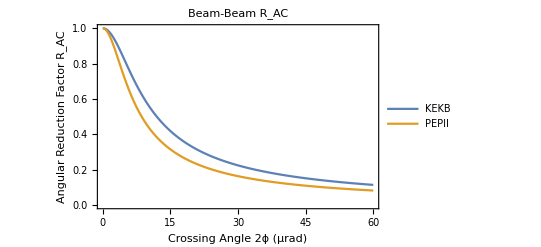

```mathematica
ListLinePlot[{Partition[Riffle[AngleDatBeam⟦All,1⟧,AngleDatBeam⟦All,2⟧],2],Partition[Riffle[AngleDatBeam⟦All,1⟧,AngleDatBeam⟦All,3⟧],2]},Frame->True,FrameLabel->{"Crossing Angle 2ϕ (μrad)","Angular Reduction Factor R_AC "},PlotLabel->"Beam-Beam R_AC",LabelStyle->15,PlotLegends->Placed[LineLegend[{"KEKB","PEPII"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

```mathematica
AngleDatCompton=Table[{ϕ/mrad,RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.DIANA680,RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.MAXIIIinjopt},{ϕ,0,40mrad,0.01mrad}];
```

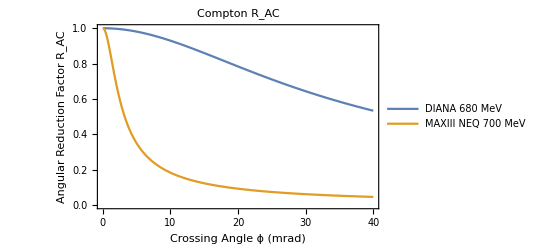

```mathematica
ListLinePlot[{Partition[Riffle[AngleDatCompton⟦All,1⟧,AngleDatCompton⟦All,2⟧],2],Partition[Riffle[AngleDatCompton⟦All,1⟧,AngleDatCompton⟦All,3⟧],2]},Frame->True,FrameLabel->{"Crossing Angle ϕ (mrad)","Angular Reduction Factor R_AC "},PlotLabel->"Compton R_AC",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA 680 MeV","MAXIII NEQ 700 MeV"},LabelStyle->12,LegendFunction->frame],{0.7,0.35}]]
```

# M. Furman Hourglass Verification (Analytical vs Numerical)

Section Notes
• Shown that there is an analytical solution for the round beams case.
• Shown that the answer given by a numerical method achieves that of the analytical case for round beams.
• Performed a convergence test which shows |t| > 2 is a good integration range. |t| = 100 will be used for future cases as a margin of error, but convergence tests are required for important results.
• The divergence laser term within the Furman function has been corrected.
• The results show a rough 4% reduction in the luminosity for the CBETA case.

## Furman Analytical Solution (Round Beams)

• The Hourglass function by furman has the form below when the two colliding beams are round i.e. t_x=t_y=t_RB. 
• We can find an analytical solution for this case which has been shown by Bruno + Werner Herr, I’ve seen it in a presentation.
• This leads us to a Furman round beams analytical calculation, which we can benchmark our numerical method against.

```mathematica
FURMANround[t_,tRB_]:=1/Sqrt[π]*Exp[-t^2]/(Sqrt[1+t^2/tRB^2]*Sqrt[1+t^2/tRB^2]);
```

```mathematica
Integrate[FURMANround[t,tRB],{t,-∞,∞},Assumptions->{Element[tRB,Reals],tRB>0}]
```

ⅇ^(tRB^2) √π tRB Erfc[tRB]

## Furman Round Beam Analytical Calculation (Compton Scattering)

• Taken x case, round beam so should be the same anyway. This way less cases need entering.

```mathematica
tRB[βIPx_,Ee_,ϵx_,σL_,σze_,σzL_,λ_]:=Sqrt[(2*(σe[βIPx,Ee,ϵx]^2+σL^2))/((σze^2+σzL^2)*(σe[βIPx,Ee,ϵx]^2/βIPx^2+σL^2/zr[σL,λ]^2))];
```

```mathematica
FURMANanalytical[βIPx_,Ee_,ϵx_,σze_,σL_,λ_,σzL_]:=Exp[tRB[βIPx,Ee,ϵx,σL,σze,σzL,λ]^2]*Sqrt[π]*tRB[βIPx,Ee,ϵx,σL,σze,σzL,λ]*Erfc[tRB[βIPx,Ee,ϵx,σL,σze,σzL,λ]];
```

```mathematica
RHGCBETAanalytical=FURMANanalytical[βIPx,Ee,ϵx,σze,σL,λ,σzL]/.CBETA150
```

0.959365

## Furman Hourglass Function (Compton Scattering)

```mathematica
txcom[βIPx_,Ee_,ϵx_,σze_,σL_,λ_,σzL_]:=Sqrt[(2*(σe[βIPx,Ee,ϵx]^2+σL^2))/((σze^2+σzL^2)*(σe[βIPx,Ee,ϵx]^2/βIPx^2+σL^2/zr[σL,λ]^2))];
```

```mathematica
tycom[βIPy_,Ee_,ϵy_,σze_,σL_,λ_,σzL_]:=Sqrt[(2*(σe[βIPy,Ee,ϵy]^2+σL^2))/((σze^2+σzL^2)*(σe[βIPy,Ee,ϵy]^2/βIPy^2+σL^2/zr[σL,λ]^2))];
```

```mathematica
FURMANcompton[t_,βIPx_,βIPy_,Ee_,ϵx_,ϵy_,σze_,σL_,λ_,σzL_]:=1/Sqrt[π]*Exp[-t^2]/(Sqrt[1+t^2/txcom[βIPx,Ee,ϵx,σze,σL,λ,σzL]^2]*Sqrt[1+t^2/tycom[βIPy,Ee,ϵy,σze,σL,λ,σzL]^2]);
```

```mathematica
RHGCBETAnumerical=NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.CBETA150,{t,-10,10}]
```

0.959365

## Furman Hourglass Function Plot (Compton Scattering)

```mathematica
FURMANfuncCBETA=Table[{t,FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.CBETA150},{t,-10,10,0.001}];
```

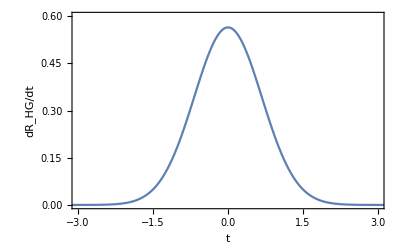

```mathematica
ListLinePlot[FURMANfuncCBETA,PlotRange->{{-3,3},{0,0.6}},Frame->True,FrameLabel->{"t","dR_HG/dt"},LabelStyle->15]
```

## Furman Hourglass Convergence Testing

```mathematica
FURMANconvergence=Table[{i,NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.CBETA150,{t,-i,i}],((RHGCBETAnumerical-NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.CBETA150,{t,-i,i}])/RHGCBETAnumerical)},{i,0,5,0.01}];
```

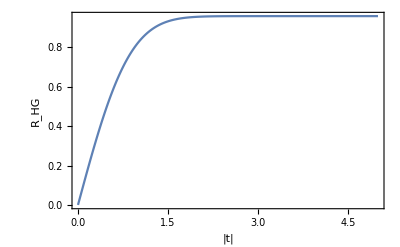

```mathematica
ListLinePlot[Partition[Riffle[FURMANconvergence⟦All,1⟧,FURMANconvergence⟦All,2⟧],2],Frame->True,FrameLabel->{"|t|","R_HG"},LabelStyle->17]
```

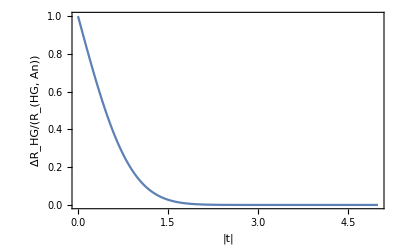

```mathematica
ListLinePlot[Partition[Riffle[FURMANconvergence⟦All,1⟧,FURMANconvergence⟦All,3⟧],2],Frame->True,FrameLabel->{"|t|","ΔR_HG/(R_(HG, An))"},LabelStyle->17,PlotRange->Full]
```

# M. Furman Hourglass Verification (Beam-Beam)

Section Notes
• The KEKB and PEPII R_HG calculations shot good agreement with the Miyahara paper. 0.36% (KEKB) and 1.49% (PEPII).
• This is a good signal that I am doing the Furman calculation correctly.

## Furman Calculation (beam - beam)

```mathematica
txbeam[βIP1x_,βIP2x_,Ee1_,Ee2_,ϵ1x_,ϵ2x_,σz1e_,σz2e_]:=Sqrt[(2*(σe[βIP1x,Ee1,ϵ1x]^2+σe[βIP2x,Ee2,ϵ2x]^2))/((σz1e^2+σz2e^2)*(σe[βIP1x,Ee1,ϵ1x]^2/βIP1x^2+σe[βIP2x,Ee2,ϵ2x]^2/βIP2x^2))];
```

```mathematica
tybeam[βIP1y_,βIP2y_,Ee1_,Ee2_,ϵ1y_,ϵ2y_,σz1e_,σz2e_]:=Sqrt[(2*(σe[βIP1y,Ee1,ϵ1y]^2+σe[βIP2y,Ee2,ϵ2y]^2))/((σz1e^2+σz2e^2)*(σe[βIP1y,Ee1,ϵ1y]^2/βIP1y^2+σe[βIP2y,Ee2,ϵ2y]^2/βIP2y^2))];
```

```mathematica
FURMANbeam[t_,βIP1x_,βIP2x_,βIP1y_,βIP2y_,Ee1_,Ee2_,ϵ1x_,ϵ2x_,ϵ1y_,ϵ2y_,σz1e_,σz2e_]:=1/Sqrt[π]*Exp[-t^2]/(Sqrt[1+t^2/txbeam[βIP1x,βIP2x,Ee1,Ee2,ϵ1x,ϵ2x,σz1e,σz2e]^2]*Sqrt[1+t^2/tybeam[βIP1y,βIP2y,Ee1,Ee2,ϵ1y,ϵ2y,σz1e,σz2e]^2]);
```

```mathematica
RHGPEPII=NIntegrate[FURMANbeam[t,βIP1x,βIP2x,βIP1y,βIP2y,Ee1,Ee2,ϵ1x,ϵ2x,ϵ1y,ϵ2y,σz1e,σz2e]/.PEPII,{t,-100,100}]
```

0.795296

```mathematica
RHGKEKB=NIntegrate[FURMANbeam[t,βIP1x,βIP2x,βIP1y,βIP2y,Ee1,Ee2,ϵ1x,ϵ2x,ϵ1y,ϵ2y,σz1e,σz2e]/.KEKB,{t,-100,100}]
```

0.844711

## Furman Hourglass Function Plot (beam - beam)

```mathematica
FURMANfuncBEAM=Table[{t,FURMANbeam[t,βIP1x,βIP2x,βIP1y,βIP2y,Ee1,Ee2,ϵ1x,ϵ2x,ϵ1y,ϵ2y,σz1e,σz2e]/.PEPII,FURMANbeam[t,βIP1x,βIP2x,βIP1y,βIP2y,Ee1,Ee2,ϵ1x,ϵ2x,ϵ1y,ϵ2y,σz1e,σz2e]/.KEKB},{t,-10,10,0.01}];
```

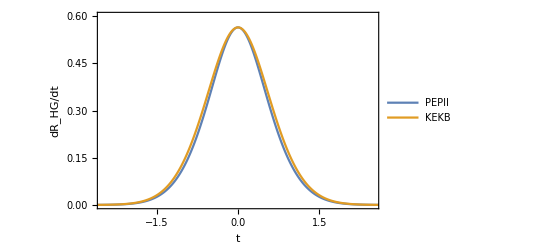

```mathematica
ListLinePlot[{Partition[Riffle[FURMANfuncBEAM⟦All,1⟧,FURMANfuncBEAM⟦All,2⟧],2],Partition[Riffle[FURMANfuncBEAM⟦All,1⟧,FURMANfuncBEAM⟦All,3⟧],2]},Frame->True,PlotRange->{{-2.5,2.5},{0,.6}},FrameLabel->{"t","dR_HG/dt"},LabelStyle->15,PlotLegends->Placed[LineLegend[{"PEPII","KEKB"},LabelStyle->12,LegendFunction->frame],{0.8,0.7}]]
```

# DIANA ERL vs MAXIII NEQ SR

Section Notes
• A factor of ~13 is lost from DIANA to MAXII NEQ from the angular crossing R_AC.
• A factor of ~2.1 is lost from DIANA to MAXIII NEQ from the hourglass effect R_HG
•A combined factor of ~27 is lost from DIANA to MAXIII NEQ from the cumulative effects of hourglass and angular crossing R_AC×R_HG
• The hourglass effect is a small effect for ERL driven ICS (4% decrease CBETA, 2% decrease DIANA), but large for SR driven ICS (53% decrease).
• The R_HGvs σ_ze plots overlap for out MAXIII NEQ and DIANA cases, this means that transverse effects at this level have a negligible effect on the hourglass effect.

## Furman Fuction Plot

```mathematica
FURMANfuncERLSR=Table[{t,FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.DIANA680,FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.MAXIIIinjopt},{t,-10,10,0.001}];
```

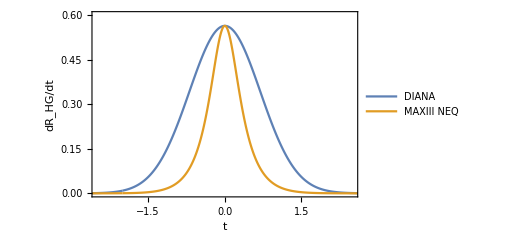

```mathematica
ListLinePlot[{Partition[Riffle[FURMANfuncERLSR⟦All,1⟧,FURMANfuncERLSR⟦All,2⟧],2],Partition[Riffle[FURMANfuncERLSR⟦All,1⟧,FURMANfuncERLSR⟦All,3⟧],2]},Frame->True,FrameLabel->{"t","dR_HG/dt "},LabelStyle->15,PlotRange->{{-2.5,2.5},{0,0.6}},PlotLegends->Placed[LineLegend[{"DIANA","MAXIII NEQ"},LabelStyle->12,LegendFunction->frame],{0.8,0.8}]]
```

## FURMAN Hourglass + Angular Correction

```mathematica
FURMANRACRHG[σze_,σzL_,βIPx_,βIPy_,Ee_,ϵx_,ϵy_,σL_,ϕ_,λ_,tval_]:=Quiet[RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]*NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL],{t,-tval,tval}]];
```

```mathematica
Quiet[FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,0,λ,10]/.DIANA680]
```

0.982907

```mathematica
Quiet[FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,40mrad,λ,10]/.DIANA680]
```

0.524674

## Reduction Factor Plots

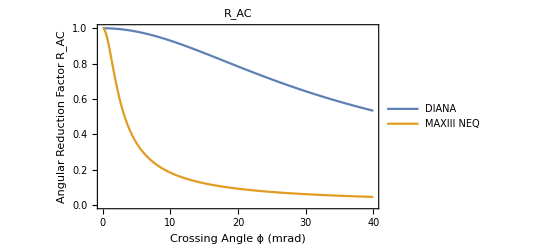

```mathematica
ListLinePlot[{Partition[Riffle[AngleDatCompton⟦All,1⟧,AngleDatCompton⟦All,2⟧],2],Partition[Riffle[AngleDatCompton⟦All,1⟧,AngleDatCompton⟦All,3⟧],2]},Frame->True,FrameLabel->{"Crossing Angle ϕ (mrad)","Angular Reduction Factor R_AC "},PlotLabel->"R_AC",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII NEQ"},LabelStyle->12,LegendFunction->frame],{0.7,0.35}]]
```

```mathematica
RHGvsσze=Table[{σze/(c*ps),NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.DIANA680,{t,-10,10}],NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.MAXIIIinjopt,{t,-10,10}]},{σze,c*0.1ps,c*100ps,c*0.1ps}];
```

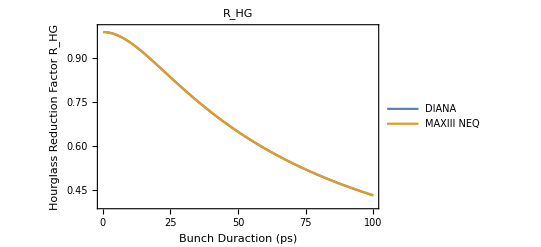

```mathematica
ListLinePlot[{Partition[Riffle[RHGvsσze⟦All,1⟧,RHGvsσze⟦All,2⟧],2],Partition[Riffle[RHGvsσze⟦All,1⟧,RHGvsσze⟦All,3⟧],2]},Frame->True,PlotRange->{{0,100},{0.4,1}},FrameLabel->{"Bunch Duraction (ps)","Hourglass Reduction Factor R_HG "},PlotLabel->"R_HG",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII NEQ"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

```mathematica
RACRHGvsσze=Quiet[Table[{σze/(c*ps),FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.DIANA680,FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.MAXIIIinjopt},{σze,c*0.1ps,c*100ps,c*0.1ps}]];
```

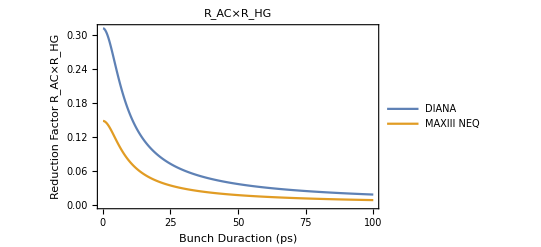

```mathematica
ListLinePlot[{Partition[Riffle[RACRHGvsσze⟦All,1⟧,RACRHGvsσze⟦All,2⟧],2],Partition[Riffle[RACRHGvsσze⟦All,1⟧,RACRHGvsσze⟦All,3⟧],2]},Frame->True,PlotRange->Full,FrameLabel->{"Bunch Duraction (ps)","Reduction Factor R_AC×R_HG "},PlotLabel->"R_AC×R_HG",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII NEQ"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

```mathematica
RACRHGvsϕ=Table[{ϕ/mrad,NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.DIANA680,{t,-10,10}]*RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.DIANA680,NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.MAXIIIinjopt,{t,-10,10}]*RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.MAXIIIinjopt},{ϕ,0,40mrad,0.1mrad}];
```

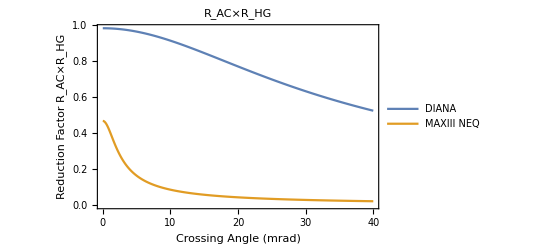

```mathematica
ListLinePlot[{Partition[Riffle[RACRHGvsϕ⟦All,1⟧,RACRHGvsϕ⟦All,2⟧],2],Partition[Riffle[RACRHGvsϕ⟦All,1⟧,RACRHGvsϕ⟦All,3⟧],2]},Frame->True,PlotRange->Full,FrameLabel->{"Crossing Angle (mrad)","Reduction Factor R_AC×R_HG "},PlotLabel->"R_AC×R_HG",LabelStyle->15,PlotLegends->Placed[LineLegend[{"DIANA","MAXIII NEQ"},LabelStyle->12,LegendFunction->frame],{0.75,0.3}]]
```

## Analytical Reduction Factor Calculations

```mathematica
RACDIANA=RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.DIANA680
```

0.277817

```mathematica
RACMAXIII=RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.MAXIIIinjopt
```

0.0214116

```mathematica
ΔRAC=RACDIANA/RACMAXIII
```

12.9751

```mathematica
RHGDIANA=NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.DIANA680,{t,-10,10}]
```

0.982907

```mathematica
RHGMAXIII=NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.MAXIIIinjopt,{t,-10,10}]
```

0.46816

```mathematica
ΔRHG=RHGDIANA/RHGMAXIII
```

2.09951

```mathematica
RACRHGDIANA=Quiet[FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.DIANA680]
```

0.273068

```mathematica
RACRHGMAXIII=Quiet[FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.MAXIIIinjopt]
```

0.010024

```mathematica
ΔRACRHG=RACRHGDIANA/RACRHGMAXIII
```

27.2414

# Miyahra Method

Section Notes
• The Miyahara method has been succesfully replicated as shown by the benchmarking. Figure 6 of his paper is correct.
• The difference between R_ACHG and R_AC×R_HG appear to be largest when the transverse size is larger i.e why the DIANA case residuals are smaller than the MAXIII NEQ residuals.
• According to Miyahara, the differences in reduction factor with bunch length between the two cases are purely arises because of the difference between the methods, not the cases themselves. This suggests R_ACHG is completely independent of transverse effects (at least small ones)

## Miyahara Intermediaries

```mathematica
H[ϕ_,βIPx_,Ee_,ϵx_,σL_,βIPy_,ϵy_,σze_,σzL_]:=Cos[ϕ/2]*Sqrt[((σe[βIPx,Ee,ϵx]^2+σL^2)*(σe[βIPy,Ee,ϵy]^2+σL^2))/(π*(σze^2+σzL^2))];
Ux[βIPx_,Ee_,ϵx_,σL_,λ_]:=Sqrt[1/2*(σe[βIPx,Ee,ϵx]^2/βIPx^2+σL^2/zr[σL,λ]^2)];
Uy[βIPy_,Ee_,ϵy_,σL_,λ_]:=Sqrt[1/2*(σe[βIPy,Ee,ϵy]^2/βIPy^2+σL^2/zr[σL,λ]^2)];
h[ϕ_,βIPx_,Ee_,ϵx_,σL_,λ_,σze_,σzL_,Zc_]:=Sin[ϕ/2]^2/((σe[βIPx,Ee,ϵx]^2+σL^2)+Ux[βIPx,Ee,ϵx,σL,λ]^2*Zc^2)+Cos[ϕ/2]^2/(σze^2+σzL^2);
```

## Miyahara R_ACHG Calculation (DIANA and MAXIII)

```mathematica
MIYAHARA[ϕ_,βIPx_,Ee_,ϵx_,σL_,βIPy_,ϵy_,σze_,σzL_,λ_,Zc_]:=(H[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL]*Exp[-h[ϕ,βIPx,Ee,ϵx,σL,λ,σze,σzL,Zc]*Zc^2])/(Sqrt[(σe[βIPx,Ee,ϵx]^2+σL^2)+Ux[βIPx,Ee,ϵx,σL,λ]^2*Zc^2]*Sqrt[(σe[βIPy,Ee,ϵy]^2+σL^2)+Uy[βIPy,Ee,ϵy,σL,λ]^2*Zc^2]);
```

```mathematica
RACHGDIANA=NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.DIANA680,{Zc,-0.1,0.1}]
```

0.277966

```mathematica
RACRHGDIANA=Quiet[FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.DIANA680]
```

0.273068

```mathematica
RACHGMAXIII=NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.MAXIIIinjopt,{Zc,-0.1,0.1}]
```

0.0214277

```mathematica
RACRHGMAXIII=Quiet[FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.MAXIIIinjopt]
```

0.010024

## Miyahara Function Plots

```mathematica
MIYAHARAfunc=Table[{Zc,MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.DIANA680,MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.MAXIIIinjopt,MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.Miyahara},{Zc,-0.002,0.002,0.00001}];
```

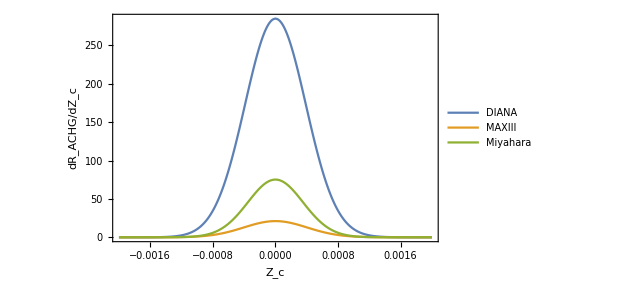

```mathematica
ListLinePlot[{Partition[Riffle[MIYAHARAfunc⟦All,1⟧,MIYAHARAfunc⟦All,2⟧],2],Partition[Riffle[MIYAHARAfunc⟦All,1⟧,MIYAHARAfunc⟦All,3⟧],2],Partition[Riffle[MIYAHARAfunc⟦All,1⟧,MIYAHARAfunc⟦All,4⟧],2]},Frame->True,PlotRange->Full,LabelStyle->15,FrameLabel->{"Z_c","dR_ACHG/dZ_c"},PlotLegends->Placed[LineLegend[{"DIANA","MAXIII","Miyahara"},LabelStyle->12,LegendFunction->frame],{0.8,0.7}]]
```

## Miyahara Benchmarking

```mathematica
MIYAHARAbench=Quiet[Table[{ϕ/mrad,RACCOMPTON[σze,σzL,βIPx,Ee,ϵx,σL,ϕ]/.Miyahara,NIntegrate[FURMANcompton[t,βIPx,βIPy,Ee,ϵx,ϵy,σze,σL,λ,σzL]/.Miyahara,{t,-10,10}],FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.Miyahara,NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.Miyahara,{Zc,-0.1,0.1}]},{ϕ,0,40mrad,0.1mrad}]];
```

```mathematica
ListLinePlot[{Partition[Riffle[MIYAHARAbench⟦All,1⟧,MIYAHARAbench⟦All,2⟧],2],Partition[Riffle[MIYAHARAbench⟦All,1⟧,MIYAHARAbench⟦All,3⟧],2],Partition[Riffle[MIYAHARAbench⟦All,1⟧,MIYAHARAbench⟦All,4⟧],2],Partition[Riffle[MIYAHARAbench⟦All,1⟧,MIYAHARAbench⟦All,5⟧],2]},Frame->True,PlotRange->{{0,40},{0,1}},PlotStyle->{{Black,Dashed},{Green,Dashed},Red,Blue},LabelStyle->15,FrameLabel->{"Crossing Angle ϕ (mrad)","Reduction Factor"},PlotLegends->Placed[LineLegend[{"R_AC","R_HG","R_AC×R_HG","R_ACHG"},LabelStyle->12,LegendFunction->frame],{0.8,0.45}]]
```

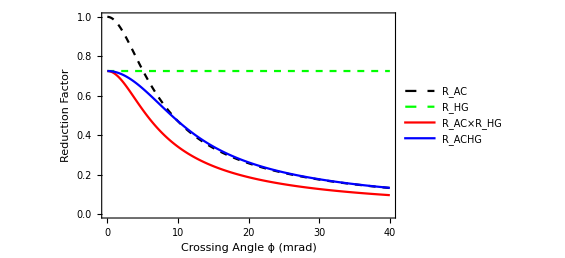
```mathematica
-Graphics--Graphics-
```

## Miyahara (R_ACHG) vs Furman + Angular Correction (R_AC×R_HG) - ϕ Investigation

```mathematica
MIYAHARAvsFURMANϕ=Quiet[Table[{(ϕ*180)/π,NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.DIANA680,{Zc,-0.1,0.1}],FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.DIANA680,NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.MAXIIIinjopt,{Zc,-0.1,0.1}],FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.MAXIIIinjopt},{ϕ,0,(10π)/180,0.2mrad}]];
```

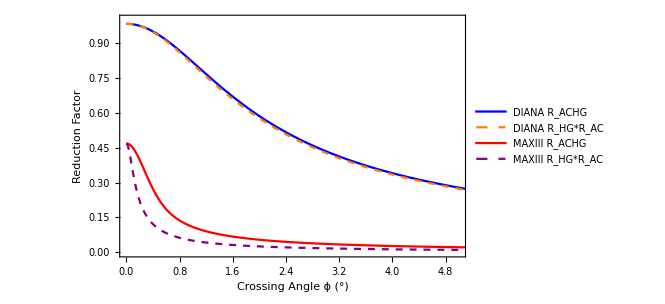

```mathematica
ListLinePlot[{Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,2⟧],2],Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,3⟧],2],Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,4⟧],2],Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,5⟧],2]},Frame->True,FrameLabel->{"Crossing Angle ϕ (°)","Reduction Factor"},LabelStyle->15,PlotStyle->{Blue,{Orange,Dashed},Red,{Purple,Dashed}},PlotRange->{{0,5},{0,1}},PlotLegends->Placed[LineLegend[{"DIANA R_ACHG","DIANA R_HG*R_AC","MAXIII R_ACHG","MAXIII R_HG*R_AC"},LabelStyle->12,LegendFunction->frame],{0.75,0.75}]]
```

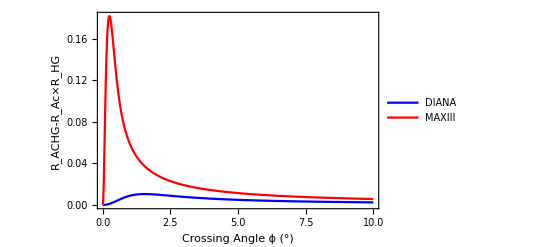

```mathematica
ListLinePlot[{Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,2⟧-MIYAHARAvsFURMANϕ⟦All,3⟧],2],Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,4⟧-MIYAHARAvsFURMANϕ⟦All,5⟧],2]},Frame->True,FrameLabel->{"Crossing Angle ϕ (°)","R_ACHG-R_Ac×R_HG"},LabelStyle->15,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{"DIANA","MAXIII"},LabelStyle->12,LegendFunction->frame],{0.75,0.75}]]
```

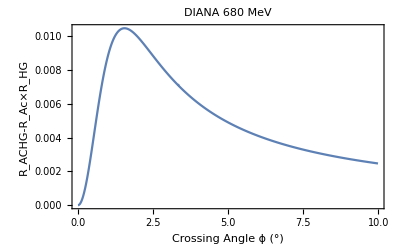

```mathematica
ListLinePlot[Partition[Riffle[MIYAHARAvsFURMANϕ⟦All,1⟧,MIYAHARAvsFURMANϕ⟦All,2⟧-MIYAHARAvsFURMANϕ⟦All,3⟧],2],Frame->True,PlotLabel->"DIANA 680 MeV",FrameLabel->{"Crossing Angle ϕ (°)","R_ACHG-R_Ac×R_HG"},LabelStyle->15,PlotRange->Full]
```

## Miyahara (R_ACHG) vs Furman + Angular Correction (R_AC×R_HG) - σ_ze Investigation

```mathematica
MIYAHARAvsFURMANσze=Quiet[Table[{σze/(c*ps),NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.DIANA680,{Zc,-0.1,0.1}],FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.DIANA680,NIntegrate[MIYAHARA[ϕ,βIPx,Ee,ϵx,σL,βIPy,ϵy,σze,σzL,λ,Zc]/.MAXIIIinjopt,{Zc,-0.1,0.1}],FURMANRACRHG[σze,σzL,βIPx,βIPy,Ee,ϵx,ϵy,σL,ϕ,λ,10]/.MAXIIIinjopt},{σze,c*0.1ps,c*100ps,c*0.1ps}]];
```

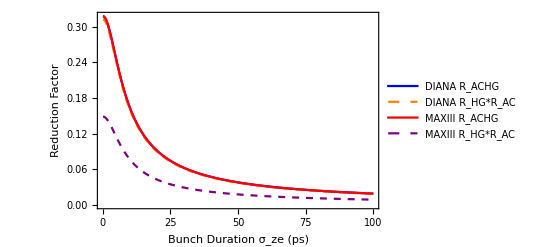

```mathematica
ListLinePlot[{Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,2⟧],2],Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,3⟧],2],Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,4⟧],2],Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,5⟧],2]},Frame->True,FrameLabel->{"Bunch Duration σ_ze (ps)","Reduction Factor"},LabelStyle->15,PlotStyle->{Blue,{Orange,Dashed},Red,{Purple,Dashed}},PlotRange->All,PlotLegends->Placed[LineLegend[{"DIANA R_ACHG","DIANA R_HG*R_AC","MAXIII R_ACHG","MAXIII R_HG*R_AC"},LabelStyle->12,LegendFunction->frame],{0.7,0.7}]]
```

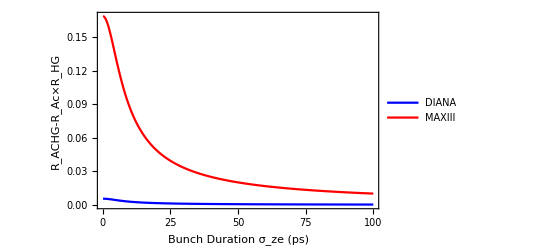

```mathematica
ListLinePlot[{Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,2⟧-MIYAHARAvsFURMANσze⟦All,3⟧],2],Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,4⟧-MIYAHARAvsFURMANσze⟦All,5⟧],2]},Frame->True,FrameLabel->{"Bunch Duration σ_ze (ps)","R_ACHG-R_Ac×R_HG"},LabelStyle->15,PlotRange->Full,PlotStyle->{Blue,Red},PlotLegends->Placed[LineLegend[{"DIANA","MAXIII"},LabelStyle->12,LegendFunction->frame],{0.75,0.75}]]
```

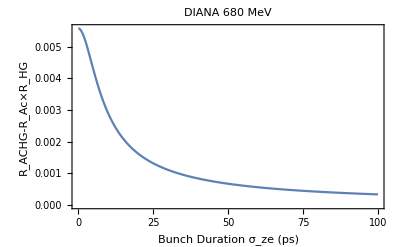

```mathematica
ListLinePlot[Partition[Riffle[MIYAHARAvsFURMANσze⟦All,1⟧,MIYAHARAvsFURMANσze⟦All,2⟧-MIYAHARAvsFURMANσze⟦All,3⟧],2],Frame->True,PlotLabel->"DIANA 680 MeV",FrameLabel->{"Bunch Duration σ_ze (ps)","R_ACHG-R_Ac×R_HG"},LabelStyle->15,PlotRange->Full]
```